Last modified on: Sunday, July 8, 2018 at 17:19

Author Info

Jaime Buitrago

Sebastian Bodenstein

Visible Impact Corporation

Poster Session Content

Authorship Identification by Using a Machine Learning Approach

Given sufficient amounts of text with the authors’ information tagged, can we accurately produce a feature vector that describes the style of the author and represents a fingerprint of its style?

Add the most representative image of your project here. (We recommend just 1 image, if you add more, we will make a collage of the images.)

-Graphics3D-

Reuters 50/50 is a database of 5000 news articles written by 50 different authors.  It serves as a baseline for authorship identification.  Several classification methods were tried in order to evaluate their accuracy.  Wolfram’s Classify function was used on full articles, sentences and normalized sentences.  The output was further processed to improve accuracy.  These results were compared with an ad-hoc neural network classifier using two different pre-trained neural networks: Glove-100 and ELMo Contextual as feature extractors, and further processing their output with various combinations of LSTM and GRL layers.  The best results, 65% accuracy,  were obtained by using Wolfram’s Classifier on the full text articles, as well as using the same function on sentences and post-processing the result using a probabilistic model.  The best published results show a classification accuracy of 69.1%.

It will be necessary to work on the parameters of the neural networks in the model.  Extensive training with the ELMo Contextual neural network will be necessary to assess its contribution to accuracy improvement.

Note: Everything above this bar is your poster.Make sure it fits on a single page. "Preview Poster"

End of School Presentation Content

In addition to the poster content, include other content to present at the 2 minute presentation for end of school. Use the buttons below to add more sections."Add Header""Add Text""Add Code or Image"

Project Workflow

-Graphics-

Classification Results

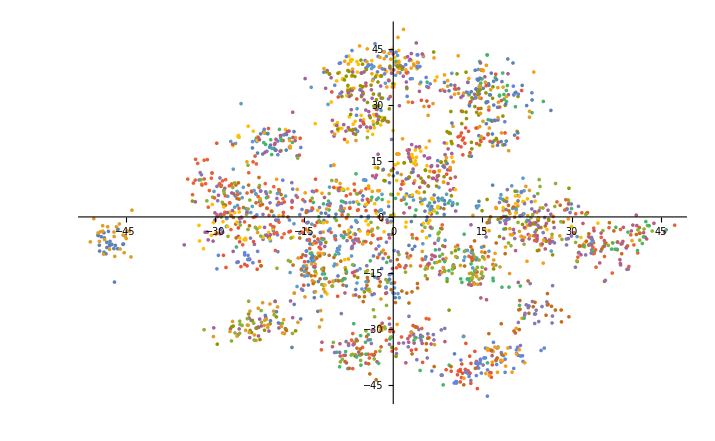
-Graphics--Graphics--Graphics-

Note: Everything above this bar is in your 2 minute presentation. Make sure it fits on 2 slides. "Preview Presentation"

Detailed Project Notes

#### Main Results in Detail

Reuters 50/50 is a database of 5000 news articles written by 50 different authors broken down into two equal sets (training and validation).  It serves as a baseline for authorship identification.  Several classification methods were tried in order to evaluate their accuracy.  Wolfram’s Classify function was used on full articles, sentences and normalized sentences.  The output was further processed to improve accuracy.  These results were compared with an ad-hoc neural network classifier using two different pre-trained neural networks: Glove-100 and ELMo Contextual as feature extractors, and further processing their output with various combinations of LSTM and GRL layers.  The best results, 65% accuracy,  were obtained by using Wolfram’s Classifier on the full text articles, as well as using the same function on sentences and post-processing the result using a probabilistic model.  The best published results show a classification accuracy of 69.1%.

#### Code

Provide one of:

Link to the GitHub

Explicit code

#### Objective

Given enough text with the authors tagged, can we accurately produce a feature vector that describes the style of the author and is a fingerprint of its style.

#### Data

Reuters 50/50 is a database of 5000 news articles written by 50 different authors broken down into two equal sets (training and validation).  It serves as a baseline for authorship identification in many research fields.

#### Methodology

The figure below shows the different tests that were carried out during this work.  A choice between using the full text form of the articles or using sentences was clear, and therefore both avenues were explored.  Since the Classifier function in Wolfram is available, it was used to provide a baseline for classification.  The prediction results of the 5 methods were compared.  Since the objective was to generate a vector set, two methods were explored:  using a neural network, and using a combination of feature extraction and dimension reduction, to produce a vector plot that would identify each article.  What s sought is a clustering of articles for the same author in this reduced feature space.

#### 1. Feature Extraction on Articles

The full author articles were used to feed the FeatureExtraction function.  As a result, a 14-dimension vector was obtained for each article.  The ReduceDimension function was used to reduce the dimensions of the article space to three.  The plot is shown below, where each author has a different color.

It is very hard to see if there are clusters that could indicate a particular author’s style.  However, when plotted separately by author, one can see that some authors indeed are classified in clusters, while others occupy a much larger space.

```mathematica
GraphicsRow[{-Graphics3D-,-Graphics3D-}]
```

-Graphics-

Feature extraction does give some measure of classification for authors’ style but it is not a definite tool.

#### 2. Classification using Full-text Articles

The Classify function was used with three different input data sets in order to determine if the accuracy improves from one to another.  In the first case, Classify is used with the full-text articles for all the authors.  The result is an accuracy of 66.4% in author identification.  The ConfusionMatrixPlot is shown below:

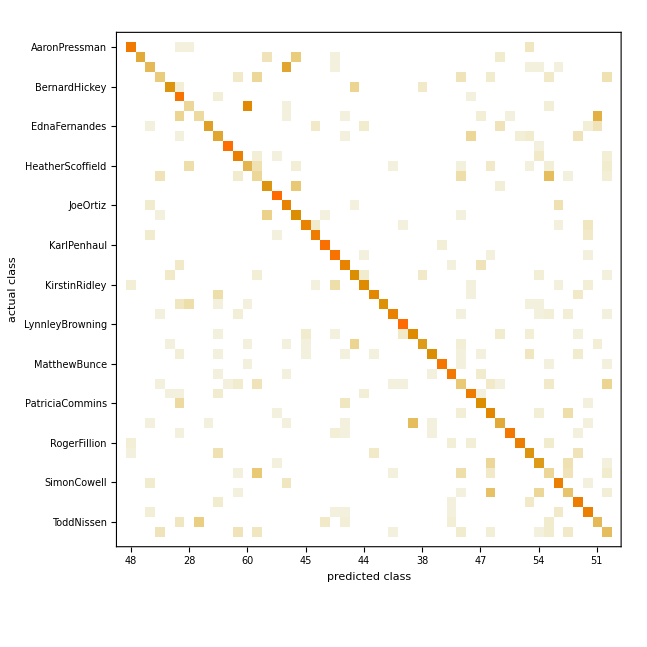

#### 3. Classification using Sentences

Each article was broken into its sentences and the resulting dataset was processed using the Classify function.  The resulting accuracy was only 38.8%, and the resulting ConfusionMatrixPlot is shown below:

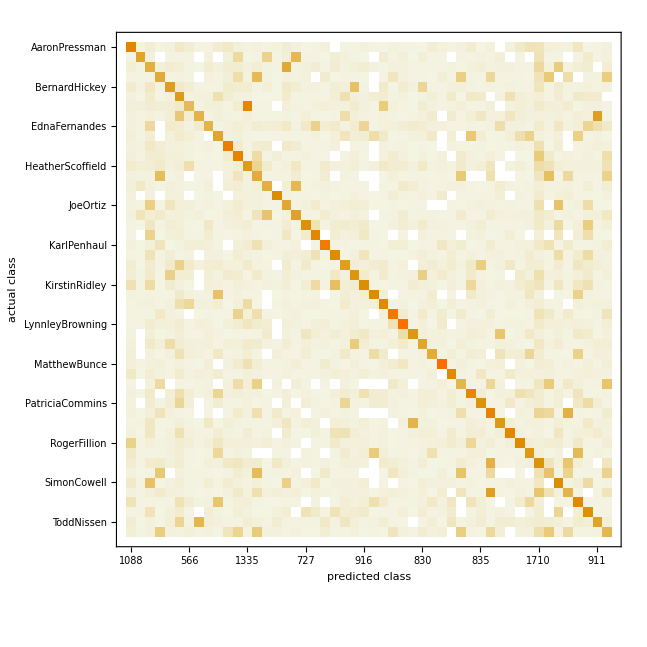

#### 4. Classification using Sentences and Postprocessing with Stochastic Model

Each sentence in each article was marked with a unique identifier in order to reassemble the articles after classification.  The resulting classified sentences were assembled back into articles keeping the prediction associated to each, and then feed a stochastic model in which the most frequent prediction was selected as the prediction for the article.  The accuracy improves greatly, giving a total classification accuracy of 65.3%.

#### 5. Classification using Normalized Sentences

Since each article has a different number of sentences, padding was used by creating a new dataset made of a random sample of equal size for each author, with a size equal the largest number of sentences in an article.  By normalizing the data the accuracy may have an improvement.  The result of this method showed an accuracy of only 39.9% with a very slight improvement over the non-normalized method.  The confusion matrix plot is shown below:

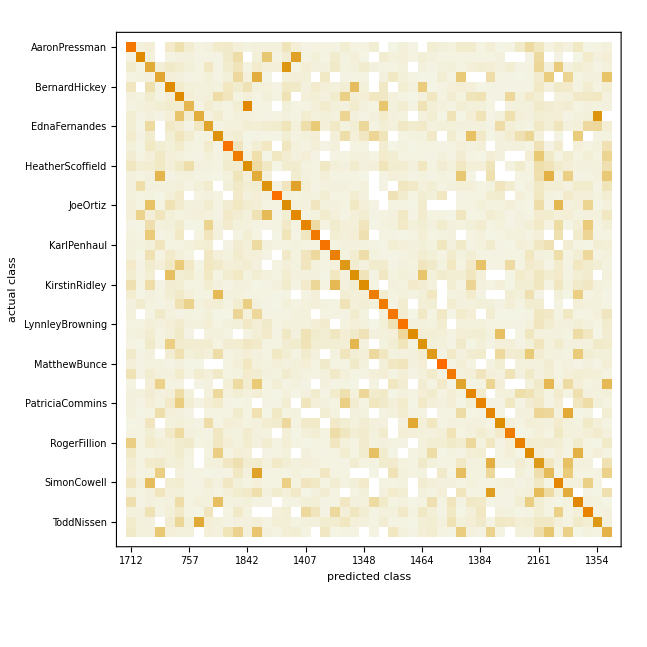

#### 6. Classification using Neural Networks

Several network architectures and parameters were tried.  The classifying network is a structure that contains:
Feature Extraction --> Vectorization --> Classifier --> Prediction.  As a Feature Extractor, two different configurations were used:

Using ELMo Contextual Word Representations Trained on 1B Word Benchmark, which is a classifier trained on 1 billion contextual words:
NetGraph[<>]

Using GloVe 100 - Dimensional Word Vectors Trained on Wikipedia and Gigaword 5 Data, which is not contextual:

```mathematica
EmbeddingLayer[<>]
```

Both feature extractors were embedded, and once trained, their weights were frozen so that no further training would occur.  
After the Feature Extraction layer, a combination of LongShortTermMemoryLayer (LSTM) and GatedRecurrentLayer (GRL) was used, and variations in the number of neurons in each layer were used.  The combinations include the use of multiple layers of each type and different sequence order for them. 

Once they were assembled the networks looked like:
NetChain[<>]
 The networks were trained and the output layer would provide a class (one of 50 authors) and during the training both the loss function and the error were monitored for convergence between the test set and the evaluation set.  Some of the networks were trained with a reduced set of inputs in order to determine convergence, others with the full data set, but none of them completed training.  Here are some examples of the configuration-training pairs:
 
Using Sentence-by-sentence Training:

NetChain[<>]NetTrainResultsObject[<>]

```mathematica
NetChain[<>]NetTrainResultsObject[<>]
```

```mathematica
NetChain[<>]NetTrainResultsObject[<>]
```

Using Full-text Articles Training:

```mathematica
NetChain[<>]
```

```mathematica
NetTrainResultsObject[<>]
```

```mathematica
NetChain[<>]NetTrainResultsObject[<>]
```

```mathematica
NetChain[<>]
```

```mathematica
NetTrainResultsObject[<>]
```

```mathematica
NetChain[<>]
```

```mathematica
NetTrainResultsObject[<>]
```

```mathematica
NetChain[<>]
```

```mathematica
NetTrainResultsObject[<>]
```

The resulting expected classification accuracy for the validation set was 40.2%.

#### Conclusions in Detail

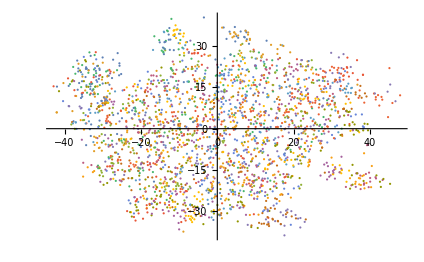
#### All Visualizations -Graphics3D--Graphics-

```mathematica
GraphicsRow[{-Graphics3D-,-Graphics3D-}]
```

-Graphics-

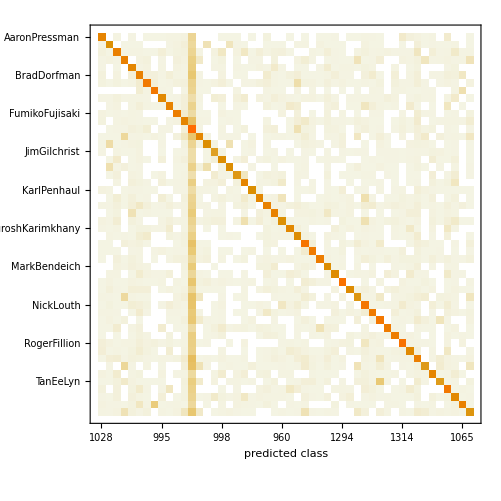

#### Data Sources Links/References

Trained neural networks were obtained from https://resources.wolframcloud.com/NeuralNetRepository/
Data was obtained from https://archive.ics.uci.edu/ml/machine-learning-databases/00217/C50.zip

#### Future Directions

It will be necessary to work on the parameters of the neural networks in the model.  Extensive training with the ELMo Contextual neural network will be necessary to assess its contribution to accuracy improvement.

#### Background Info Links/References

Chen Qian, Tianchang He,  Rao Zhang, Deep Learning based Autorship Identification, https://web.stanford.edu/class/cs224n/reports/2760185.pdf

#### Keywords

Provide keywords as items

authorship identification

deep learning

classify

#### Other information